## Numeical trial

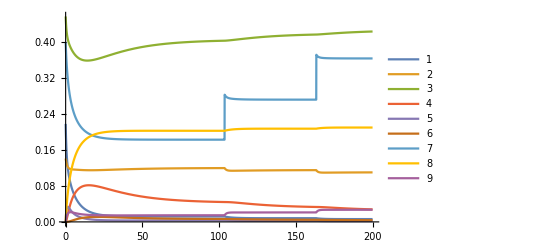

```mathematica
Clear["Global`*"];

des={x[1]'[t],x[2]'[t],x[3]'[t],x[4]'[t],x[5]'[t],x[6]'[t],x[7]'[t],x[8]'[t],x[9]'[t]}=={-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[3] x[5][t]-k[7] x[1][t] x[7][t]+k[8] x[8][t],-k[4] x[2][t] x[4][t]+k[5] x[6][t]+k[6] x[6][t]-k[9] x[2][t] x[7][t]+k[10] x[9][t],-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[6] x[6][t],-k[4] x[2][t] x[4][t]+k[3] x[5][t]+k[5] x[6][t],k[1] x[1][t] x[3][t]-k[2] x[5][t]-k[3] x[5][t],k[4] x[2][t] x[4][t]-k[5] x[6][t]-k[6] x[6][t],-k[7] x[1][t] x[7][t]-k[9] x[2][t] x[7][t]+k[8] x[8][t]+k[10] x[9][t],k[7] x[1][t] x[7][t]-k[8] x[8][t],k[9] x[2][t] x[7][t]-k[10] x[9][t]};

init={T[1],T[2],T[3],0,0,0,T[4],0,0};

vars=Array[x,9];
dvars=Thread[Derivative[1][vars]];

Block[{k,T,ssthreshold},k[n_]:=k[n]=(SeedRandom[n];RandomReal[]);
T[n_]:=T[n]=(SeedRandom[n+10];RandomReal[]);
ssthreshold=1.*^-4;
(*Print[des];*)(*to see the ODE*){sol}=NDSolve[{des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,x[7][t]->x[7][t]+0.1]]},vars,{t,0,200},MaxSteps->100000]];

Plot@@{Through[vars[t]]/.sol,Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->Automatic}
```

## Analytical solution trial

```mathematica
Solve[Table[0,{i,Length[des[[1]]]}]==des[[2]],Table[x[i][t],{i,Length[des[[1]]]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[3][t]→((k[2]+k[3]) x[5][t])/(k[1] x[1][t]),x[4][t]→(k[3] (k[5]+k[6]) x[5][t])/(k[4] k[6] x[2][t]),x[6][t]→(k[3] x[5][t])/k[6],x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[4][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[2][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→0},{x[2][t]→0,x[3][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→0}}

Here we have substitution:

{(k[2]+k[3])/k[1]→km[1],(k[5]+k[6])/k[4]→km[2],k[3]/k[6]→kcr,k[7]/k[8]→kd[1],k[9]/k[10]→kd[2]}

```mathematica
solution={x[3]->(km[1]x[5])/x[1],x[4]->(kcr*km[2] x[5])/x[2],x[6]->kcr x[5],x[8]->kd[1] x[1]x[7],x[9]->kd[2] x[2] x[7]}
```

{x[3]→(km[1] x[5])/x[1],x[4]→(kcr km[2] x[5])/x[2],x[6]→kcr x[5],x[8]→kd[1] x[1] x[7],x[9]→kd[2] x[2] x[7]}

Here we have

{T[1]==x[1]+x[5]+x[8],T[2]==x[2]+x[6]+x[9],T[3]==x[3]+x[4]+x[5]+x[6],T[4]==x[7]+x[8]+x[9]}

## Continue

```mathematica
t4={T[4]==x[7]+(kd[2] km[2] T[2] x[7])/(km[2]+x[4]+kd[2] km[2] x[7])-(kd[1] x[7] (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7]))/((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))}
```

{T[4]==x[7]+(kd[2] km[2] T[2] x[7])/(km[2]+x[4]+kd[2] km[2] x[7])-(kd[1] x[7] (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7]))/((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))}

```mathematica
t42=Collect[ExpandAll[{((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))*(km[2]+x[4]+kd[2] km[2] x[7])*T[4]==((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))*(km[2]+x[4]+kd[2] km[2] x[7])*x[7]+((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))*kd[2] km[2] T[2] x[7]-((km[2]+x[4]+kd[2] km[2] x[7])*kd[1] x[7] (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7]))}],{x[4],x[7]}]
```

{km[2]^2 T[4]+(kd[1] km[2]^2 T[4]+2 kd[2] km[2]^2 T[4]) x[7]+(2 kd[1] kd[2] km[2]^2 T[4]+kd[2]^2 km[2]^2 T[4]) x[7]^2+kd[1] kd[2]^2 km[2]^2 T[4] x[7]^3+x[4]^2 (T[4]+kd[1] T[4] x[7])+x[4] (2 km[2] T[4]+(2 kd[1] km[2] T[4]+2 kd[2] km[2] T[4]) x[7]+2 kd[1] kd[2] km[2] T[4] x[7]^2)==(km[2]^2+kd[1] km[2]^2 T[1]+kd[2] km[2]^2 T[2]) x[7]+(kd[1] km[2]^2+2 kd[2] km[2]^2+2 kd[1] kd[2] km[2]^2 T[1]+kd[1] kd[2] km[2]^2 T[2]+kd[2]^2 km[2]^2 T[2]) x[7]^2+(2 kd[1] kd[2] km[2]^2+kd[2]^2 km[2]^2+kd[1] kd[2]^2 km[2]^2 T[1]+kd[1] kd[2]^2 km[2]^2 T[2]) x[7]^3+kd[1] kd[2]^2 km[2]^2 x[7]^4+x[4]^2 ((1+kd[1] T[1]-kcr kd[1] T[2]) x[7]+kd[1] x[7]^2)+x[4] ((2 km[2]+2 kd[1] km[2] T[1]-kcr kd[1] km[2] T[2]+kd[2] km[2] T[2]) x[7]+(2 kd[1] km[2]+2 kd[2] km[2]+2 kd[1] kd[2] km[2] T[1]+kd[1] kd[2] km[2] T[2]-kcr kd[1] kd[2] km[2] T[2]) x[7]^2+2 kd[1] kd[2] km[2] x[7]^3)}

```mathematica
Collect[km[2]^2 T[4]+(kd[1] km[2]^2 T[4]+2 kd[2] km[2]^2 T[4]) x[7]+(2 kd[1] kd[2] km[2]^2 T[4]+kd[2]^2 km[2]^2 T[4]) x[7]^2+kd[1] kd[2]^2 km[2]^2 T[4] x[7]^3+x[4]^2 (T[4]+kd[1] T[4] x[7])+x[4] (2 km[2] T[4]+(2 kd[1] km[2] T[4]+2 kd[2] km[2] T[4]) x[7]+2 kd[1] kd[2] km[2] T[4] x[7]^2)-((km[2]^2+kd[1] km[2]^2 T[1]+kd[2] km[2]^2 T[2]) x[7]+(kd[1] km[2]^2+2 kd[2] km[2]^2+2 kd[1] kd[2] km[2]^2 T[1]+kd[1] kd[2] km[2]^2 T[2]+kd[2]^2 km[2]^2 T[2]) x[7]^2+(2 kd[1] kd[2] km[2]^2+kd[2]^2 km[2]^2+kd[1] kd[2]^2 km[2]^2 T[1]+kd[1] kd[2]^2 km[2]^2 T[2]) x[7]^3+kd[1] kd[2]^2 km[2]^2 x[7]^4+x[4]^2 ((1+kd[1] T[1]-kcr kd[1] T[2]) x[7]+kd[1] x[7]^2)+x[4] ((2 km[2]+2 kd[1] km[2] T[1]-kcr kd[1] km[2] T[2]+kd[2] km[2] T[2]) x[7]+(2 kd[1] km[2]+2 kd[2] km[2]+2 kd[1] kd[2] km[2] T[1]+kd[1] kd[2] km[2] T[2]-kcr kd[1] kd[2] km[2] T[2]) x[7]^2+2 kd[1] kd[2] km[2] x[7]^3)),{x[4],x[7]}]
```

km[2]^2 T[4]+(-km[2]^2-kd[1] km[2]^2 T[1]-kd[2] km[2]^2 T[2]+kd[1] km[2]^2 T[4]+2 kd[2] km[2]^2 T[4]) x[7]+(-kd[1] km[2]^2-2 kd[2] km[2]^2-2 kd[1] kd[2] km[2]^2 T[1]-kd[1] kd[2] km[2]^2 T[2]-kd[2]^2 km[2]^2 T[2]+2 kd[1] kd[2] km[2]^2 T[4]+kd[2]^2 km[2]^2 T[4]) x[7]^2+(-2 kd[1] kd[2] km[2]^2-kd[2]^2 km[2]^2-kd[1] kd[2]^2 km[2]^2 T[1]-kd[1] kd[2]^2 km[2]^2 T[2]+kd[1] kd[2]^2 km[2]^2 T[4]) x[7]^3-kd[1] kd[2]^2 km[2]^2 x[7]^4+x[4]^2 (T[4]+(-1-kd[1] T[1]+kcr kd[1] T[2]+kd[1] T[4]) x[7]-kd[1] x[7]^2)+x[4] (2 km[2] T[4]+(-2 km[2]-2 kd[1] km[2] T[1]+kcr kd[1] km[2] T[2]-kd[2] km[2] T[2]+2 kd[1] km[2] T[4]+2 kd[2] km[2] T[4]) x[7]+(-2 kd[1] km[2]-2 kd[2] km[2]-2 kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kcr kd[1] kd[2] km[2] T[2]+2 kd[1] kd[2] km[2] T[4]) x[7]^2-2 kd[1] kd[2] km[2] x[7]^3)

```mathematica
Simplify[km[2]^2 T[4]+(-km[2]^2-kd[1] km[2]^2 T[1]-kd[2] km[2]^2 T[2]+kd[1] km[2]^2 T[4]+2 kd[2] km[2]^2 T[4]) x[7]+(-kd[1] km[2]^2-2 kd[2] km[2]^2-2 kd[1] kd[2] km[2]^2 T[1]-kd[1] kd[2] km[2]^2 T[2]-kd[2]^2 km[2]^2 T[2]+2 kd[1] kd[2] km[2]^2 T[4]+kd[2]^2 km[2]^2 T[4]) x[7]^2+(-2 kd[1] kd[2] km[2]^2-kd[2]^2 km[2]^2-kd[1] kd[2]^2 km[2]^2 T[1]-kd[1] kd[2]^2 km[2]^2 T[2]+kd[1] kd[2]^2 km[2]^2 T[4]) x[7]^3-kd[1] kd[2]^2 km[2]^2 x[7]^4+x[4]^2 (T[4]+(-1-kd[1] T[1]+kcr kd[1] T[2]+kd[1] T[4]) x[7]-kd[1] x[7]^2)+x[4] (2 km[2] T[4]+(-2 km[2]-2 kd[1] km[2] T[1]+kcr kd[1] km[2] T[2]-kd[2] km[2] T[2]+2 kd[1] km[2] T[4]+2 kd[2] km[2] T[4]) x[7]+(-2 kd[1] km[2]-2 kd[2] km[2]-2 kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kcr kd[1] kd[2] km[2] T[2]+2 kd[1] kd[2] km[2] T[4]) x[7]^2-2 kd[1] kd[2] km[2] x[7]^3)]
```

-(km[2]+x[4]+kd[2] km[2] x[7]) (x[4] (-T[4] (1+kd[1] x[7])+x[7] (1+kd[1] (T[1]-kcr T[2]+x[7])))+km[2] (-T[4] (1+kd[1] x[7]) (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])+kd[1] (T[1] (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7]))))))

```mathematica
FullSimplify[x[4] (-T[4] (1+kd[1] x[7])+x[7] (1+kd[1] (T[1]-kcr T[2]+x[7])))+km[2] (-T[4] (1+kd[1] x[7]) (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])+kd[1] (T[1] (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])))))]
```

x[4] (-T[4] (1+kd[1] x[7])+x[7] (1+kd[1] (T[1]-kcr T[2]+x[7])))+km[2] (-T[4] (1+kd[1] x[7]) (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])+kd[1] (T[1]+x[7]+kd[2] (T[1]+T[2]) x[7]+kd[2] x[7]^2)))

```mathematica
t3={T[3]==x[4]+(T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])+(kcr T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])-(kcr km[1] T[2] x[4] (1+kd[1] x[7]))/(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])}
```

{T[3]==x[4]+(T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])+(kcr T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])-(kcr km[1] T[2] x[4] (1+kd[1] x[7]))/(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])}

```mathematica
t32=Collect[ExpandAll[{(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*T[3]==(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*x[4]+(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*T[2] x[4]+(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*kcr T[2] x[4]-(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*kcr km[1] T[2] x[4] (1+kd[1] x[7])}],{x[4],x[7]}]
```

{-km[2]^3 T[1] T[3]+(-T[1] T[3]+kcr T[2] T[3]) x[4]^3-3 kd[2] km[2]^3 T[1] T[3] x[7]-3 kd[2]^2 km[2]^3 T[1] T[3] x[7]^2-kd[2]^3 km[2]^3 T[1] T[3] x[7]^3+x[4]^2 (-3 km[2] T[1] T[3]+2 kcr km[2] T[2] T[3]+(-3 kd[2] km[2] T[1] T[3]+2 kcr kd[2] km[2] T[2] T[3]) x[7])+x[4] (-3 km[2]^2 T[1] T[3]+kcr km[2]^2 T[2] T[3]+(-6 kd[2] km[2]^2 T[1] T[3]+2 kcr kd[2] km[2]^2 T[2] T[3]) x[7]+(-3 kd[2]^2 km[2]^2 T[1] T[3]+kcr kd[2]^2 km[2]^2 T[2] T[3]) x[7]^2)==(-T[1]+kcr T[2]) x[4]^4+x[4]^3 (-3 km[2] T[1]-kcr km[1] T[2]+2 kcr km[2] T[2]-T[1] T[2]-kcr T[1] T[2]+kcr T[2]^2+kcr^2 T[2]^2+(-3 kd[2] km[2] T[1]-kcr kd[1] km[1] T[2]+2 kcr kd[2] km[2] T[2]) x[7])+x[4]^2 (-3 km[2]^2 T[1]-2 kcr km[1] km[2] T[2]+kcr km[2]^2 T[2]-2 km[2] T[1] T[2]-2 kcr km[2] T[1] T[2]+kcr km[2] T[2]^2+kcr^2 km[2] T[2]^2+(-6 kd[2] km[2]^2 T[1]-2 kcr kd[1] km[1] km[2] T[2]-2 kcr kd[2] km[1] km[2] T[2]+2 kcr kd[2] km[2]^2 T[2]-2 kd[2] km[2] T[1] T[2]-2 kcr kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[2]^2+kcr^2 kd[2] km[2] T[2]^2) x[7]+(-3 kd[2]^2 km[2]^2 T[1]-2 kcr kd[1] kd[2] km[1] km[2] T[2]+kcr kd[2]^2 km[2]^2 T[2]) x[7]^2)+x[4] (-km[2]^3 T[1]-kcr km[1] km[2]^2 T[2]-km[2]^2 T[1] T[2]-kcr km[2]^2 T[1] T[2]+(-3 kd[2] km[2]^3 T[1]-kcr kd[1] km[1] km[2]^2 T[2]-2 kcr kd[2] km[1] km[2]^2 T[2]-2 kd[2] km[2]^2 T[1] T[2]-2 kcr kd[2] km[2]^2 T[1] T[2]) x[7]+(-3 kd[2]^2 km[2]^3 T[1]-2 kcr kd[1] kd[2] km[1] km[2]^2 T[2]-kcr kd[2]^2 km[1] km[2]^2 T[2]-kd[2]^2 km[2]^2 T[1] T[2]-kcr kd[2]^2 km[2]^2 T[1] T[2]) x[7]^2+(-kd[2]^3 km[2]^3 T[1]-kcr kd[1] kd[2]^2 km[1] km[2]^2 T[2]) x[7]^3)}

```mathematica
Collect[-km[2]^3 T[1] T[3]+(-T[1] T[3]+kcr T[2] T[3]) x[4]^3-3 kd[2] km[2]^3 T[1] T[3] x[7]-3 kd[2]^2 km[2]^3 T[1] T[3] x[7]^2-kd[2]^3 km[2]^3 T[1] T[3] x[7]^3+x[4]^2 (-3 km[2] T[1] T[3]+2 kcr km[2] T[2] T[3]+(-3 kd[2] km[2] T[1] T[3]+2 kcr kd[2] km[2] T[2] T[3]) x[7])+x[4] (-3 km[2]^2 T[1] T[3]+kcr km[2]^2 T[2] T[3]+(-6 kd[2] km[2]^2 T[1] T[3]+2 kcr kd[2] km[2]^2 T[2] T[3]) x[7]+(-3 kd[2]^2 km[2]^2 T[1] T[3]+kcr kd[2]^2 km[2]^2 T[2] T[3]) x[7]^2)-((-T[1]+kcr T[2]) x[4]^4+x[4]^3 (-3 km[2] T[1]-kcr km[1] T[2]+2 kcr km[2] T[2]-T[1] T[2]-kcr T[1] T[2]+kcr T[2]^2+kcr^2 T[2]^2+(-3 kd[2] km[2] T[1]-kcr kd[1] km[1] T[2]+2 kcr kd[2] km[2] T[2]) x[7])+x[4]^2 (-3 km[2]^2 T[1]-2 kcr km[1] km[2] T[2]+kcr km[2]^2 T[2]-2 km[2] T[1] T[2]-2 kcr km[2] T[1] T[2]+kcr km[2] T[2]^2+kcr^2 km[2] T[2]^2+(-6 kd[2] km[2]^2 T[1]-2 kcr kd[1] km[1] km[2] T[2]-2 kcr kd[2] km[1] km[2] T[2]+2 kcr kd[2] km[2]^2 T[2]-2 kd[2] km[2] T[1] T[2]-2 kcr kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[2]^2+kcr^2 kd[2] km[2] T[2]^2) x[7]+(-3 kd[2]^2 km[2]^2 T[1]-2 kcr kd[1] kd[2] km[1] km[2] T[2]+kcr kd[2]^2 km[2]^2 T[2]) x[7]^2)+x[4] (-km[2]^3 T[1]-kcr km[1] km[2]^2 T[2]-km[2]^2 T[1] T[2]-kcr km[2]^2 T[1] T[2]+(-3 kd[2] km[2]^3 T[1]-kcr kd[1] km[1] km[2]^2 T[2]-2 kcr kd[2] km[1] km[2]^2 T[2]-2 kd[2] km[2]^2 T[1] T[2]-2 kcr kd[2] km[2]^2 T[1] T[2]) x[7]+(-3 kd[2]^2 km[2]^3 T[1]-2 kcr kd[1] kd[2] km[1] km[2]^2 T[2]-kcr kd[2]^2 km[1] km[2]^2 T[2]-kd[2]^2 km[2]^2 T[1] T[2]-kcr kd[2]^2 km[2]^2 T[1] T[2]) x[7]^2+(-kd[2]^3 km[2]^3 T[1]-kcr kd[1] kd[2]^2 km[1] km[2]^2 T[2]) x[7]^3)),{x[4],x[7]}]
```

-km[2]^3 T[1] T[3]+(T[1]-kcr T[2]) x[4]^4-3 kd[2] km[2]^3 T[1] T[3] x[7]-3 kd[2]^2 km[2]^3 T[1] T[3] x[7]^2-kd[2]^3 km[2]^3 T[1] T[3] x[7]^3+x[4]^3 (3 km[2] T[1]+kcr km[1] T[2]-2 kcr km[2] T[2]+T[1] T[2]+kcr T[1] T[2]-kcr T[2]^2-kcr^2 T[2]^2-T[1] T[3]+kcr T[2] T[3]+(3 kd[2] km[2] T[1]+kcr kd[1] km[1] T[2]-2 kcr kd[2] km[2] T[2]) x[7])+x[4]^2 (3 km[2]^2 T[1]+2 kcr km[1] km[2] T[2]-kcr km[2]^2 T[2]+2 km[2] T[1] T[2]+2 kcr km[2] T[1] T[2]-kcr km[2] T[2]^2-kcr^2 km[2] T[2]^2-3 km[2] T[1] T[3]+2 kcr km[2] T[2] T[3]+(6 kd[2] km[2]^2 T[1]+2 kcr kd[1] km[1] km[2] T[2]+2 kcr kd[2] km[1] km[2] T[2]-2 kcr kd[2] km[2]^2 T[2]+2 kd[2] km[2] T[1] T[2]+2 kcr kd[2] km[2] T[1] T[2]-kcr kd[2] km[2] T[2]^2-kcr^2 kd[2] km[2] T[2]^2-3 kd[2] km[2] T[1] T[3]+2 kcr kd[2] km[2] T[2] T[3]) x[7]+(3 kd[2]^2 km[2]^2 T[1]+2 kcr kd[1] kd[2] km[1] km[2] T[2]-kcr kd[2]^2 km[2]^2 T[2]) x[7]^2)+x[4] (km[2]^3 T[1]+kcr km[1] km[2]^2 T[2]+km[2]^2 T[1] T[2]+kcr km[2]^2 T[1] T[2]-3 km[2]^2 T[1] T[3]+kcr km[2]^2 T[2] T[3]+(3 kd[2] km[2]^3 T[1]+kcr kd[1] km[1] km[2]^2 T[2]+2 kcr kd[2] km[1] km[2]^2 T[2]+2 kd[2] km[2]^2 T[1] T[2]+2 kcr kd[2] km[2]^2 T[1] T[2]-6 kd[2] km[2]^2 T[1] T[3]+2 kcr kd[2] km[2]^2 T[2] T[3]) x[7]+(3 kd[2]^2 km[2]^3 T[1]+2 kcr kd[1] kd[2] km[1] km[2]^2 T[2]+kcr kd[2]^2 km[1] km[2]^2 T[2]+kd[2]^2 km[2]^2 T[1] T[2]+kcr kd[2]^2 km[2]^2 T[1] T[2]-3 kd[2]^2 km[2]^2 T[1] T[3]+kcr kd[2]^2 km[2]^2 T[2] T[3]) x[7]^2+(kd[2]^3 km[2]^3 T[1]+kcr kd[1] kd[2]^2 km[1] km[2]^2 T[2]) x[7]^3)

```mathematica
Simplify[-km[2]^3 T[1] T[3]+(T[1]-kcr T[2]) x[4]^4-3 kd[2] km[2]^3 T[1] T[3] x[7]-3 kd[2]^2 km[2]^3 T[1] T[3] x[7]^2-kd[2]^3 km[2]^3 T[1] T[3] x[7]^3+x[4]^3 (3 km[2] T[1]+kcr km[1] T[2]-2 kcr km[2] T[2]+T[1] T[2]+kcr T[1] T[2]-kcr T[2]^2-kcr^2 T[2]^2-T[1] T[3]+kcr T[2] T[3]+(3 kd[2] km[2] T[1]+kcr kd[1] km[1] T[2]-2 kcr kd[2] km[2] T[2]) x[7])+x[4]^2 (3 km[2]^2 T[1]+2 kcr km[1] km[2] T[2]-kcr km[2]^2 T[2]+2 km[2] T[1] T[2]+2 kcr km[2] T[1] T[2]-kcr km[2] T[2]^2-kcr^2 km[2] T[2]^2-3 km[2] T[1] T[3]+2 kcr km[2] T[2] T[3]+(6 kd[2] km[2]^2 T[1]+2 kcr kd[1] km[1] km[2] T[2]+2 kcr kd[2] km[1] km[2] T[2]-2 kcr kd[2] km[2]^2 T[2]+2 kd[2] km[2] T[1] T[2]+2 kcr kd[2] km[2] T[1] T[2]-kcr kd[2] km[2] T[2]^2-kcr^2 kd[2] km[2] T[2]^2-3 kd[2] km[2] T[1] T[3]+2 kcr kd[2] km[2] T[2] T[3]) x[7]+(3 kd[2]^2 km[2]^2 T[1]+2 kcr kd[1] kd[2] km[1] km[2] T[2]-kcr kd[2]^2 km[2]^2 T[2]) x[7]^2)+x[4] (km[2]^3 T[1]+kcr km[1] km[2]^2 T[2]+km[2]^2 T[1] T[2]+kcr km[2]^2 T[1] T[2]-3 km[2]^2 T[1] T[3]+kcr km[2]^2 T[2] T[3]+(3 kd[2] km[2]^3 T[1]+kcr kd[1] km[1] km[2]^2 T[2]+2 kcr kd[2] km[1] km[2]^2 T[2]+2 kd[2] km[2]^2 T[1] T[2]+2 kcr kd[2] km[2]^2 T[1] T[2]-6 kd[2] km[2]^2 T[1] T[3]+2 kcr kd[2] km[2]^2 T[2] T[3]) x[7]+(3 kd[2]^2 km[2]^3 T[1]+2 kcr kd[1] kd[2] km[1] km[2]^2 T[2]+kcr kd[2]^2 km[1] km[2]^2 T[2]+kd[2]^2 km[2]^2 T[1] T[2]+kcr kd[2]^2 km[2]^2 T[1] T[2]-3 kd[2]^2 km[2]^2 T[1] T[3]+kcr kd[2]^2 km[2]^2 T[2] T[3]) x[7]^2+(kd[2]^3 km[2]^3 T[1]+kcr kd[1] kd[2]^2 km[1] km[2]^2 T[2]) x[7]^3)]
```

(km[2]+x[4]+kd[2] km[2] x[7]) (-km[2]^2 T[1] (T[3]-x[4]) (1+kd[2] x[7])^2+km[2] x[4] (1+kd[2] x[7]) (T[1] (T[2]-2 T[3]+2 x[4])+kcr T[2] (km[1]+T[1]+T[3]-x[4]+kd[1] km[1] x[7]))+x[4]^2 (-kcr^2 T[2]^2+T[1] (T[2]-T[3]+x[4])+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4]+kd[1] km[1] x[7])))

```mathematica
FullSimplify[-km[2]^2 T[1] (T[3]-x[4]) (1+kd[2] x[7])^2+km[2] x[4] (1+kd[2] x[7]) (T[1] (T[2]-2 T[3]+2 x[4])+kcr T[2] (km[1]+T[1]+T[3]-x[4]+kd[1] km[1] x[7]))+x[4]^2 (-kcr^2 T[2]^2+T[1] (T[2]-T[3]+x[4])+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4]+kd[1] km[1] x[7]))]
```

-km[2]^2 T[1] (T[3]-x[4]) (1+kd[2] x[7])^2+km[2] x[4] (1+kd[2] x[7]) (T[1] (T[2]-2 T[3]+2 x[4])+kcr T[2] (km[1]+T[1]+T[3]-x[4]+kd[1] km[1] x[7]))+x[4]^2 (-kcr^2 T[2]^2+T[1] (T[2]-T[3]+x[4])+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4]+kd[1] km[1] x[7]))

```mathematica
simpT4=Collect[{x[4] (-T[4] (1+kd[1] x[7])+x[7] (1+kd[1] (T[1]-kcr T[2]+x[7])))+km[2] (-T[4] (1+kd[1] x[7]) (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])+kd[1] (T[1]+x[7]+kd[2] (T[1]+T[2]) x[7]+kd[2] x[7]^2)))==0},{x[4],x[7]}]
```

{-km[2] T[4]+(km[2]+kd[1] km[2] T[1]+kd[2] km[2] T[2]-kd[1] km[2] T[4]-kd[2] km[2] T[4]) x[7]+(kd[1] km[2]+kd[2] km[2]+kd[1] kd[2] km[2] (T[1]+T[2])-kd[1] kd[2] km[2] T[4]) x[7]^2+kd[1] kd[2] km[2] x[7]^3+x[4] (-T[4]+(1+kd[1] T[1]-kcr kd[1] T[2]-kd[1] T[4]) x[7]+kd[1] x[7]^2)==0}

```mathematica
subSimpT4={-c[1]+c[2]x[7]+c[3]x[7]^2+c[4]x[7]^3-c[5]x[4]+c[6]x[4]x[7]+c[7]x[4]x[7]^2==0}
```

{-c[1]-c[5] x[4]+c[2] x[7]+c[6] x[4] x[7]+c[3] x[7]^2+c[7] x[4] x[7]^2+c[4] x[7]^3==0}

```mathematica
simpT3=Collect[{-km[2]^2 T[1] (T[3]-x[4]) (1+kd[2] x[7])^2+km[2] x[4] (1+kd[2] x[7]) (T[1] (T[2]-2 T[3]+2 x[4])+kcr T[2] (km[1]+T[1]+T[3]-x[4]+kd[1] km[1] x[7]))+x[4]^2 (-kcr^2 T[2]^2+T[1] (T[2]-T[3]+x[4])+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4]+kd[1] km[1] x[7]))==0},{x[4],x[7]}]
```

{-km[2]^2 T[1] T[3]+(T[1]-kcr T[2]) x[4]^3-2 kd[2] km[2]^2 T[1] T[3] x[7]-kd[2]^2 km[2]^2 T[1] T[3] x[7]^2+x[4]^2 (2 km[2] T[1]+kcr km[1] T[2]-kcr km[2] T[2]+T[1] T[2]+kcr T[1] T[2]-kcr T[2]^2-kcr^2 T[2]^2-T[1] T[3]+kcr T[2] T[3]+(2 kd[2] km[2] T[1]+kcr kd[1] km[1] T[2]-kcr kd[2] km[2] T[2]) x[7])+x[4] (km[2]^2 T[1]+kcr km[1] km[2] T[2]+km[2] T[1] T[2]+kcr km[2] T[1] T[2]-2 km[2] T[1] T[3]+kcr km[2] T[2] T[3]+(2 kd[2] km[2]^2 T[1]+kcr kd[1] km[1] km[2] T[2]+kcr kd[2] km[1] km[2] T[2]+kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[1] T[2]-2 kd[2] km[2] T[1] T[3]+kcr kd[2] km[2] T[2] T[3]) x[7]+(kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2]) x[7]^2)==0}

```mathematica
subSimpT3={-t[1]+t[2]*t[4]^3-t[3]x[7]-t[4]x[7]^2+t[5]x[4]^2+t[6]x[4]^2x[7]+t[7]x[4]+t[8]x[4]x[7]+t[9]x[7]^2==0}
```

{-t[1]+t[2] t[4]^3+t[7] x[4]+t[5] x[4]^2-t[3] x[7]+t[8] x[4] x[7]+t[6] x[4]^2 x[7]-t[4] x[7]^2+t[9] x[7]^2==0}

```mathematica
Solve[simpT4,x[4]]
```

{{x[4]→(km[2] T[4]-km[2] x[7]-kd[1] km[2] T[1] x[7]-kd[2] km[2] T[2] x[7]+kd[1] km[2] T[4] x[7]+kd[2] km[2] T[4] x[7]-kd[1] km[2] x[7]^2-kd[2] km[2] x[7]^2-kd[1] kd[2] km[2] T[1] x[7]^2-kd[1] kd[2] km[2] T[2] x[7]^2+kd[1] kd[2] km[2] T[4] x[7]^2-kd[1] kd[2] km[2] x[7]^3)/(-T[4]+x[7]+kd[1] T[1] x[7]-kcr kd[1] T[2] x[7]-kd[1] T[4] x[7]+kd[1] x[7]^2)}}

```mathematica
FullSimplify[(km[2] T[4]-km[2] x[7]-kd[1] km[2] T[1] x[7]-kd[2] km[2] T[2] x[7]+kd[1] km[2] T[4] x[7]+kd[2] km[2] T[4] x[7]-kd[1] km[2] x[7]^2-kd[2] km[2] x[7]^2-kd[1] kd[2] km[2] T[1] x[7]^2-kd[1] kd[2] km[2] T[2] x[7]^2+kd[1] kd[2] km[2] T[4] x[7]^2-kd[1] kd[2] km[2] x[7]^3)/(-T[4]+x[7]+kd[1] T[1] x[7]-kcr kd[1] T[2] x[7]-kd[1] T[4] x[7]+kd[1] x[7]^2)]
```

(km[2] (-T[4] (1+kd[1] x[7]) (1+kd[2] x[7])+x[7] (1+kd[2] (T[2]+x[7])+kd[1] (T[1]+x[7]+kd[2] (T[1]+T[2]) x[7]+kd[2] x[7]^2))))/(T[4] (1+kd[1] x[7])-x[7] (1+kd[1] (T[1]-kcr T[2]+x[7])))

```mathematica
t3Sol=Solve[t3,x[7]]
```

{{x[7]→(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))},{x[7]→(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))}}

The following is substituting the first solution of x[7]: (-b-√(b^2-4ac))/(2a)

```mathematica
t4Inv1=t4/.t3Sol[[1]][[1]]
```

{T[4]==(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))+(kd[2] km[2] T[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))-(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))) (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-(kd[2] km[2] T[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (1+(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2-√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))}

The following is the second solution (-b+√(b^2-4ac))/(2a), as we studied that the system is monostable thus the following is inverse function of solution x[4], T_4==f(x_4). And this function should also be monotone. Suppose this solution is positive real then √(b^2-4ac) should be positive real.

-b=2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2

```mathematica
Simplify[2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2]
```

-kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (T[3]-x[4])+x[4] (-kcr T[2] (km[1]+T[1]+T[3]-x[4])-T[1] (T[2]-2 T[3]+2 x[4])))

And we have the non-trivial solution of inverse function of solution x[4].

```mathematica
t4Inv2=t4/.t3Sol[[2]]
```

{T[4]==(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))+(kd[2] km[2] T[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))-(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))) (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-(kd[2] km[2] T[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (1+(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))}

```mathematica
Simplify[(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))+(kd[2] km[2] T[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))-(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))) (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-(kd[2] km[2] T[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (1+(kd[1] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))) (km[2]+x[4]+(kd[2] km[2] (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))))]
```

((2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√(-4 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (km[2]^2 T[1] (-T[3]+x[4])+x[4]^2 (-kcr^2 T[2]^2+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4])+T[1] (T[2]-T[3]+x[4]))+km[2] x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4])))+(kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (-T[3]+x[4])+x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4]))))^2)) (1+(2 kd[2] km[2] T[2] (kd[2] km[2] T[1] (T[3]-x[4])-kcr kd[1] km[1] T[2] x[4]))/(-kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]-kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2-√(-4 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (km[2]^2 T[1] (-T[3]+x[4])+x[4]^2 (-kcr^2 T[2]^2+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4])+T[1] (T[2]-T[3]+x[4]))+km[2] x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4])))+(kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (-T[3]+x[4])+x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4]))))^2))-(2 kd[1] kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (kcr kd[1] km[1] km[2] T[1] T[2] x[4]-kcr kd[2] km[1] km[2] T[1] T[2] x[4]-kd[2] km[2] T[1]^2 T[2] x[4]-kcr kd[2] km[2] T[1]^2 T[2] x[4]+kcr kd[2] km[2] T[1] T[2] T[3] x[4]+kcr kd[1] km[1] T[1] T[2] x[4]^2-kcr kd[2] km[2] T[1] T[2] x[4]^2-2 kcr^2 kd[1] km[1] T[2]^2 x[4]^2+T[1] √(-4 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (km[2]^2 T[1] (-T[3]+x[4])+x[4]^2 (-kcr^2 T[2]^2+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4])+T[1] (T[2]-T[3]+x[4]))+km[2] x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4])))+(kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (-T[3]+x[4])+x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4]))))^2)))/((kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]+kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√(-4 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (km[2]^2 T[1] (-T[3]+x[4])+x[4]^2 (-kcr^2 T[2]^2+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4])+T[1] (T[2]-T[3]+x[4]))+km[2] x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4])))+(kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (-T[3]+x[4])+x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4]))))^2)) (-2 kd[1] kd[2] km[2]^2 T[1] T[3]+2 kd[2]^2 km[2]^2 T[1] T[3]+2 kd[1] kd[2] km[2]^2 T[1] x[4]-2 kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1]^2 km[1] km[2] T[2] x[4]-kcr kd[1] kd[2] km[1] km[2] T[2] x[4]+kd[1] kd[2] km[2] T[1] T[2] x[4]+kcr kd[1] kd[2] km[2] T[1] T[2] x[4]-2 kd[1] kd[2] km[2] T[1] T[3] x[4]+kcr kd[1] kd[2] km[2] T[2] T[3] x[4]+2 kd[1] kd[2] km[2] T[1] x[4]^2+kcr kd[1]^2 km[1] T[2] x[4]^2-kcr kd[1] kd[2] km[2] T[2] x[4]^2-kd[1] √(-4 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])) (km[2]^2 T[1] (-T[3]+x[4])+x[4]^2 (-kcr^2 T[2]^2+kcr T[2] (km[1]+T[1]-T[2]+T[3]-x[4])+T[1] (T[2]-T[3]+x[4]))+km[2] x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4])))+(kcr kd[1] km[1] T[2] x[4] (km[2]+x[4])+kd[2] km[2] (2 km[2] T[1] (-T[3]+x[4])+x[4] (kcr T[2] (km[1]+T[1]+T[3]-x[4])+T[1] (T[2]-2 T[3]+2 x[4]))))^2)))))/(2 kd[2] km[2] (kcr kd[1] km[1] T[2] x[4]+kd[2] km[2] T[1] (-T[3]+x[4])))

Here we

If we don’t substitue T_4only consider relationship between x_4 and x_7. Then we will have ts3Sol[[2]] as the inverse function of solution x_4.

```mathematica
t3Sol[[2]]
```

{x[7]→(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))}

```mathematica
f=(2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]));
```

```mathematica
D[f,{x[4],2}]
```

(-4 kd[2] km[2] T[1]-2 kcr kd[1] km[1] T[2]+2 kcr kd[2] km[2] T[2]-(-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (km[2]^2 T[1]+kcr km[1] km[2] T[2]+km[2] T[1] T[2]+kcr km[2] T[1] T[2]-2 km[2] T[1] T[3]+kcr km[2] T[2] T[3]+4 km[2] T[1] x[4]+2 kcr km[1] T[2] x[4]-2 kcr km[2] T[2] x[4]+2 T[1] T[2] x[4]+2 kcr T[1] T[2] x[4]-2 kcr T[2]^2 x[4]-2 kcr^2 T[2]^2 x[4]-2 T[1] T[3] x[4]+2 kcr T[2] T[3] x[4]+3 T[1] x[4]^2-3 kcr T[2] x[4]^2)+2 (2 kd[2] km[2]^2 T[1]+kcr kd[1] km[1] km[2] T[2]+kcr kd[2] km[1] km[2] T[2]+kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[1] T[2]-2 kd[2] km[2] T[1] T[3]+kcr kd[2] km[2] T[2] T[3]+4 kd[2] km[2] T[1] x[4]+2 kcr kd[1] km[1] T[2] x[4]-2 kcr kd[2] km[2] T[2] x[4]) (-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)-4 (kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))^2/(4 ((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))^(3/2))+(2 (2 kd[2] km[2]^2 T[1]+kcr kd[1] km[1] km[2] T[2]+kcr kd[2] km[1] km[2] T[2]+kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[1] T[2]-2 kd[2] km[2] T[1] T[3]+kcr kd[2] km[2] T[2] T[3]+4 kd[2] km[2] T[1] x[4]+2 kcr kd[1] km[1] T[2] x[4]-2 kcr kd[2] km[2] T[2] x[4])^2-4 (4 km[2] T[1]+2 kcr km[1] T[2]-2 kcr km[2] T[2]+2 T[1] T[2]+2 kcr T[1] T[2]-2 kcr T[2]^2-2 kcr^2 T[2]^2-2 T[1] T[3]+2 kcr T[2] T[3]+6 T[1] x[4]-6 kcr T[2] x[4]) (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4])-8 (kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2]) (km[2]^2 T[1]+kcr km[1] km[2] T[2]+km[2] T[1] T[2]+kcr km[2] T[1] T[2]-2 km[2] T[1] T[3]+kcr km[2] T[2] T[3]+4 km[2] T[1] x[4]+2 kcr km[1] T[2] x[4]-2 kcr km[2] T[2] x[4]+2 T[1] T[2] x[4]+2 kcr T[1] T[2] x[4]-2 kcr T[2]^2 x[4]-2 kcr^2 T[2]^2 x[4]-2 T[1] T[3] x[4]+2 kcr T[2] T[3] x[4]+3 T[1] x[4]^2-3 kcr T[2] x[4]^2)+2 (4 kd[2] km[2] T[1]+2 kcr kd[1] km[1] T[2]-2 kcr kd[2] km[2] T[2]) (-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2))/(2 √((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(2 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]))-((kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2]) (-2 kd[2] km[2]^2 T[1]-kcr kd[1] km[1] km[2] T[2]-kcr kd[2] km[1] km[2] T[2]-kd[2] km[2] T[1] T[2]-kcr kd[2] km[2] T[1] T[2]+2 kd[2] km[2] T[1] T[3]-kcr kd[2] km[2] T[2] T[3]-4 kd[2] km[2] T[1] x[4]-2 kcr kd[1] km[1] T[2] x[4]+2 kcr kd[2] km[2] T[2] x[4]+(-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (km[2]^2 T[1]+kcr km[1] km[2] T[2]+km[2] T[1] T[2]+kcr km[2] T[1] T[2]-2 km[2] T[1] T[3]+kcr km[2] T[2] T[3]+4 km[2] T[1] x[4]+2 kcr km[1] T[2] x[4]-2 kcr km[2] T[2] x[4]+2 T[1] T[2] x[4]+2 kcr T[1] T[2] x[4]-2 kcr T[2]^2 x[4]-2 kcr^2 T[2]^2 x[4]-2 T[1] T[3] x[4]+2 kcr T[2] T[3] x[4]+3 T[1] x[4]^2-3 kcr T[2] x[4]^2)+2 (2 kd[2] km[2]^2 T[1]+kcr kd[1] km[1] km[2] T[2]+kcr kd[2] km[1] km[2] T[2]+kd[2] km[2] T[1] T[2]+kcr kd[2] km[2] T[1] T[2]-2 kd[2] km[2] T[1] T[3]+kcr kd[2] km[2] T[2] T[3]+4 kd[2] km[2] T[1] x[4]+2 kcr kd[1] km[1] T[2] x[4]-2 kcr kd[2] km[2] T[2] x[4]) (-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)-4 (kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))/(2 √((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3)))))/(-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4])^2+((kd[2]^2 km[2]^2 T[1]+kcr kd[1] kd[2] km[1] km[2] T[2])^2 (2 kd[2] km[2]^2 T[1] T[3]-2 kd[2] km[2]^2 T[1] x[4]-kcr kd[1] km[1] km[2] T[2] x[4]-kcr kd[2] km[1] km[2] T[2] x[4]-kd[2] km[2] T[1] T[2] x[4]-kcr kd[2] km[2] T[1] T[2] x[4]+2 kd[2] km[2] T[1] T[3] x[4]-kcr kd[2] km[2] T[2] T[3] x[4]-2 kd[2] km[2] T[1] x[4]^2-kcr kd[1] km[1] T[2] x[4]^2+kcr kd[2] km[2] T[2] x[4]^2+√((-2 kd[2] km[2]^2 T[1] T[3]+2 kd[2] km[2]^2 T[1] x[4]+kcr kd[1] km[1] km[2] T[2] x[4]+kcr kd[2] km[1] km[2] T[2] x[4]+kd[2] km[2] T[1] T[2] x[4]+kcr kd[2] km[2] T[1] T[2] x[4]-2 kd[2] km[2] T[1] T[3] x[4]+kcr kd[2] km[2] T[2] T[3] x[4]+2 kd[2] km[2] T[1] x[4]^2+kcr kd[1] km[1] T[2] x[4]^2-kcr kd[2] km[2] T[2] x[4]^2)^2-4 (-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4]) (-km[2]^2 T[1] T[3]+km[2]^2 T[1] x[4]+kcr km[1] km[2] T[2] x[4]+km[2] T[1] T[2] x[4]+kcr km[2] T[1] T[2] x[4]-2 km[2] T[1] T[3] x[4]+kcr km[2] T[2] T[3] x[4]+2 km[2] T[1] x[4]^2+kcr km[1] T[2] x[4]^2-kcr km[2] T[2] x[4]^2+T[1] T[2] x[4]^2+kcr T[1] T[2] x[4]^2-kcr T[2]^2 x[4]^2-kcr^2 T[2]^2 x[4]^2-T[1] T[3] x[4]^2+kcr T[2] T[3] x[4]^2+T[1] x[4]^3-kcr T[2] x[4]^3))))/(-kd[2]^2 km[2]^2 T[1] T[3]+kd[2]^2 km[2]^2 T[1] x[4]+kcr kd[1] kd[2] km[1] km[2] T[2] x[4])^3